```mathematica
ClearAll["Global`*"]
```

## Mo100

```mathematica
enBMMo={-0.9000000000,-0.8000000000,-0.7000000000,-0.6000000000,-0.5000000000,-0.4000000000,-0.3000000000,-0.2000000000,-0.1000000000,0.0000000000,0.1000000000,0.2000000000,0.3000000000,0.4000000000,0.5000000000,0.6000000000,0.7000000000,0.8000000000,0.9000000000,1.0000000000,1.1000000000,1.2000000000,1.3000000000,1.4000000000,1.5000000000,1.6000000000,1.7000000000,1.8000000000,1.9000000000,2.0000000000,2.1000000000,2.2000000000,2.3000000000,2.4000000000,2.5000000000,2.6000000000,2.7000000000,2.8000000000,2.9000000000,3.0000000000,3.1000000000,3.2000000000,3.3000000000,3.4000000000,3.5000000000,3.6000000000,3.7000000000,3.8000000000,3.9000000000,4.0000000000,4.1000000000,4.2000000000,4.3000000000,4.4000000000,4.5000000000,4.6000000000,4.7000000000,4.8000000000,4.9000000000,5.0000000000,5.1000000000,5.2000000000,5.3000000000,5.4000000000,5.5000000000,5.6000000000,5.7000000000,5.8000000000,5.9000000000,6.0000000000,6.1000000000,6.2000000000,6.3000000000,6.4000000000,6.5000000000,6.6000000000,6.7000000000,6.8000000000,6.9000000000,7.0000000000,7.1000000000,7.2000000000,7.3000000000,7.4000000000,7.5000000000,7.6000000000,7.7000000000,7.8000000000,7.9000000000,8.0000000000,8.1000000000,8.2000000000,8.3000000000,8.4000000000,8.5000000000,8.6000000000,8.7000000000,8.8000000000,8.9000000000,9.0000000000,9.1000000000,9.2000000000,9.3000000000,9.4000000000,9.5000000000,9.6000000000,9.7000000000,9.8000000000,9.9000000000,10.0000000000,10.1000000000,10.2000000000,10.3000000000,10.4000000000,10.5000000000,10.6000000000,10.7000000000,10.8000000000,10.9000000000,11.0000000000,11.1000000000,11.2000000000,11.3000000000,11.4000000000,11.5000000000,11.6000000000,11.7000000000,11.8000000000,11.9000000000,12.0000000000,12.1000000000,12.2000000000,12.3000000000,12.4000000000,12.5000000000,12.6000000000,12.7000000000,12.8000000000,12.9000000000,13.0000000000,13.1000000000,13.2000000000,13.3000000000,13.4000000000,13.5000000000,13.6000000000,13.7000000000,13.8000000000,13.9000000000,14.0000000000,14.1000000000,14.2000000000,14.3000000000,14.4000000000,14.5000000000,14.6000000000,14.7000000000,14.8000000000,14.9000000000,15.0000000000,15.1000000000,15.2000000000,15.3000000000,15.4000000000,15.5000000000,15.6000000000,15.7000000000,15.8000000000,15.9000000000,16.0000000000,16.1000000000,16.2000000000,16.3000000000,16.4000000000,16.5000000000,16.6000000000,16.7000000000,16.8000000000,16.9000000000,17.0000000000,17.1000000000,17.2000000000,17.3000000000,17.4000000000,17.5000000000,17.6000000000,17.7000000000,17.8000000000,17.9000000000,18.0000000000,18.1000000000,18.2000000000,18.3000000000,18.4000000000,18.5000000000,18.6000000000,18.7000000000,18.8000000000,18.9000000000,19.0000000000,19.1000000000,19.2000000000,19.3000000000,19.4000000000,19.5000000000,19.6000000000,19.7000000000,19.8000000000,19.9000000000,20.0000000000,20.1000000000,20.2000000000,20.3000000000,20.4000000000,20.5000000000,20.6000000000,20.7000000000,20.8000000000,20.9000000000,21.0000000000};
strBMMo={0.0000005742,0.0000018275,0.0000055095,0.0000157333,0.0000425608,0.0001090740,0.0002648455,0.0006093559,0.0013286536,0.0027458783,0.0053797185,0.0099940919,0.0176096235,0.0294389376,0.0467123445,0.0703858848,0.1007698054,0.1371691903,0.1776645578,0.2191523247,0.2577017643,0.2891824478,0.3100150402,0.3178451039,0.3119601510,0.2933547471,0.2644576067,0.2286229747,0.1895287729,0.1506157710,0.1146636712,0.0835524083,0.0582132782,0.0387398086,0.0246047479,0.0149197034,0.0086793596,0.0049503843,0.0029889618,0.0022915998,0.0025953227,0.0038448983,0.0061408392,0.0096796502,0.0147032940,0.0214898411,0.0304366880,0.0422989439,0.0586306295,0.0824175420,0.1187803364,0.1754792193,0.2628161861,0.3924910846,0.5751226518,0.8165554327,1.1136874158,1.4511601390,1.8005168776,2.1230463984,2.3764254310,2.5237794888,2.5425493197,2.4302438709,2.2050643063,1.9011783537,1.5603162845,1.2225045942,0.9187104694,0.6671016672,0.4731392777,0.3324909253,0.2351870633,0.1695640246,0.1250844059,0.0937627811,0.0704074346,0.0521221289,0.0375237972,0.0260098754,0.0172446949,0.0108939778,0.0065514124,0.0037731846,0.0021484313,0.0013632569,0.0012444461,0.0017859460,0.0031643362,0.0057421181,0.0100458898,0.0166979366,0.0262821985,0.0391442400,0.0551583711,0.0735321153,0.0927388142,0.1106533611,0.1249071806,0.1333930895,0.1347756810,0.1288387059,0.1165473762,0.0998049213,0.0809936696,0.0624604237,0.0461053727,0.0331709338,0.0242380738,0.0193655364,0.0182791040,0.0205353406,0.0256280873,0.0330490905,0.0423344542,0.0531181736,0.0651820048,0.0784598244,0.0929496755,0.1085211867,0.1246697030,0.1403276113,0.1538571133,0.1632945741,0.1668096646,0.1632332328,0.1524557023,0.1355358617,0.1144731443,0.0917292387,0.0696730862,0.0501304803,0.0341533454,0.0220259501,0.0134438130,0.0077649862,0.0042437702,0.0021944765,0.0010736462,0.0004969714,0.0002176378,0.0000901705,0.0000353443,0.0000131068,0.0000045983,0.0000015262,0.0000004792,0.0000001424,0.0000000400,0.0000000106,0.0000000027,0.0000000006,0.0000000001,0.0000000000,0.0000000001,0.0000000004,0.0000000022,0.0000000103,0.0000000458,0.0000001928,0.0000007670,0.0000028876,0.0000102844,0.0000346532,0.0001104645,0.0003331350,0.0009504633,0.0025654767,0.0065511629,0.0158265526,0.0361719442,0.0782122859,0.1599910569,0.3096235857,0.5668784722,0.9818914844,1.6089947349,2.4943842332,3.6583873176,5.0761402552,6.6633886395,8.2751195212,9.7223445214,10.8065069852,11.3636348684,11.3049020351,10.6398115551,9.4736790882,7.9803327999,6.3597630745,4.7948880419,3.4200590589,2.3078434237,1.4733186145,0.8898250171,0.5084288051,0.2748357879,0.1405510261,0.0680005394,0.0311249237,0.0134778877,0.0055214478,0.0021399406,0.0007846357,0.0002721774,0.0000893210,0.0000277315,0.0000081453,0.0000022634,0.0000005950,0.0000001480,0.0000000348,0.0000000078,0.0000000016,0.0000000003,0.0000000001,0.0000000000,0.0000000000,0.0000000000,0.0000000000};
enBPMo={-0.9000000000,-0.8000000000,-0.7000000000,-0.6000000000,-0.5000000000,-0.4000000000,-0.3000000000,-0.2000000000,-0.1000000000,0.0000000000,0.1000000000,0.2000000000,0.3000000000,0.4000000000,0.5000000000,0.6000000000,0.7000000000,0.8000000000,0.9000000000,1.0000000000,1.1000000000,1.2000000000,1.3000000000,1.4000000000,1.5000000000,1.6000000000,1.7000000000,1.8000000000,1.9000000000,2.0000000000,2.1000000000,2.2000000000,2.3000000000,2.4000000000,2.5000000000,2.6000000000,2.7000000000,2.8000000000,2.9000000000,3.0000000000,3.1000000000,3.2000000000,3.3000000000,3.4000000000,3.5000000000,3.6000000000,3.7000000000,3.8000000000,3.9000000000,4.0000000000,4.1000000000,4.2000000000,4.3000000000,4.4000000000,4.5000000000,4.6000000000,4.7000000000,4.8000000000,4.9000000000,5.0000000000,5.1000000000,5.2000000000,5.3000000000,5.4000000000,5.5000000000,5.6000000000,5.7000000000,5.8000000000,5.9000000000,6.0000000000,6.1000000000,6.2000000000,6.3000000000,6.4000000000,6.5000000000,6.6000000000,6.7000000000,6.8000000000,6.9000000000,7.0000000000,7.1000000000,7.2000000000,7.3000000000,7.4000000000,7.5000000000,7.6000000000,7.7000000000,7.8000000000,7.9000000000,8.0000000000,8.1000000000,8.2000000000,8.3000000000,8.4000000000,8.5000000000,8.6000000000,8.7000000000,8.8000000000,8.9000000000,9.0000000000,9.1000000000,9.2000000000,9.3000000000,9.4000000000,9.5000000000,9.6000000000,9.7000000000,9.8000000000,9.9000000000,10.0000000000,10.1000000000,10.2000000000,10.3000000000,10.4000000000,10.5000000000,10.6000000000,10.7000000000,10.8000000000,10.9000000000,11.0000000000,11.1000000000,11.2000000000,11.3000000000,11.4000000000,11.5000000000,11.6000000000,11.7000000000,11.8000000000,11.9000000000,12.0000000000,12.1000000000,12.2000000000,12.3000000000,12.4000000000,12.5000000000,12.6000000000,12.7000000000,12.8000000000,12.9000000000,13.0000000000,13.1000000000,13.2000000000,13.3000000000,13.4000000000,13.5000000000,13.6000000000,13.7000000000,13.8000000000,13.9000000000,14.0000000000,14.1000000000,14.2000000000,14.3000000000,14.4000000000,14.5000000000,14.6000000000,14.7000000000,14.8000000000,14.9000000000,15.0000000000,15.1000000000,15.2000000000,15.3000000000,15.4000000000,15.5000000000,15.6000000000,15.7000000000,15.8000000000,15.9000000000,16.0000000000,16.1000000000,16.2000000000,16.3000000000,16.4000000000,16.5000000000,16.6000000000,16.7000000000,16.8000000000,16.9000000000,17.0000000000,17.1000000000,17.2000000000,17.3000000000,17.4000000000,17.5000000000,17.6000000000,17.7000000000,17.8000000000,17.9000000000,18.0000000000,18.1000000000,18.2000000000,18.3000000000,18.4000000000,18.5000000000,18.6000000000,18.7000000000,18.8000000000,18.9000000000,19.0000000000,19.1000000000,19.2000000000,19.3000000000,19.4000000000,19.5000000000,19.6000000000,19.7000000000,19.8000000000,19.9000000000,20.0000000000,20.1000000000,20.2000000000,20.3000000000,20.4000000000,20.5000000000,20.6000000000,20.7000000000,20.8000000000,20.9000000000,21.0000000000};
strBPMo={0.0000000577,0.0000001425,0.0000003337,0.0000007409,0.0000015602,0.0000031169,0.0000059095,0.0000106378,0.0000181911,0.0000295746,0.0000457624,0.0000675025,0.0000951345,0.0001285156,0.0001671390,0.0002104626,0.0002583496,0.0003113949,0.0003708608,0.0004380334,0.0005130536,0.0005935930,0.0006739790,0.0007453591,0.0007971649,0.0008196013,0.0008063769,0.0007566895,0.0006757112,0.0005733869,0.0004620090,0.0003534407,0.0002568780,0.0001777035,0.0001175053,0.0000749395,0.0000469432,0.0000298666,0.0000202718,0.0000153506,0.0000130389,0.0000119529,0.0000112532,0.0000105016,0.0000095365,0.0000083725,0.0000071192,0.0000059197,0.0000049057,0.0000041706,0.0000037580,0.0000036628,0.0000038401,0.0000042202,0.0000047258,0.0000052889,0.0000058660,0.0000064468,0.0000070542,0.0000077335,0.0000085316,0.0000094708,0.0000105268,0.0000116167,0.0000126077,0.0000133453,0.0000136964,0.0000135975,0.0000130946,0.0000123665,0.0000117264,0.0000116053,0.0000125184,0.0000150163,0.0000196171,0.0000267147,0.0000364635,0.0000486562,0.0000626292,0.0000772434,0.0000909831,0.0001021880,0.0001093851,0.0001116419,0.0001088387,0.0001017712,0.0000920473,0.0000818063,0.0000733349,0.0000686703,0.0000692581,0.0000757023,0.0000876221,0.0001036360,0.0001214992,0.0001384198,0.0001515388,0.0001584943,0.0001579309,0.0001497980,0.0001353339,0.0001167285,0.0000965714,0.0000772589,0.0000605327,0.0000472596,0.0000374704,0.0000305903,0.0000257544,0.0000221017,0.0000189744,0.0000159986,0.0000130621,0.0000102291,0.0000076388,0.0000054209,0.0000036486,0.0000023266,0.0000014046,0.0000008026,0.0000004340,0.0000002220,0.0000001075,0.0000000492,0.0000000213,0.0000000087,0.0000000034,0.0000000012,0.0000000004,0.0000000001,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000001,0.0000000004,0.0000000014,0.0000000045,0.0000000135,0.0000000383,0.0000001029,0.0000002615,0.0000006286,0.0000014296,0.0000030762,0.0000062620,0.0000120595,0.0000219719,0.0000378724,0.0000617582,0.0000952763,0.0001390570,0.0001920075,0.0002508194,0.0003099714,0.0003624097,0.0004008626,0.0004194777,0.0004152788,0.0003889451,0.0003446311,0.0002888938,0.0002291076,0.0001718931,0.0001220099,0.0000819312,0.0000520500,0.0000312831,0.0000177876,0.0000095685,0.0000048695,0.0000023445,0.0000010679,0.0000004602,0.0000001876,0.0000000724,0.0000000264,0.0000000091,0.0000000030,0.0000000009,0.0000000003,0.0000000001,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000};
```

## Ru100

```mathematica
enBPRu={-0.9000000000,-0.8000000000,-0.7000000000,-0.6000000000,-0.5000000000,-0.4000000000,-0.3000000000,-0.2000000000,-0.1000000000,0.0000000000,0.1000000000,0.2000000000,0.3000000000,0.4000000000,0.5000000000,0.6000000000,0.7000000000,0.8000000000,0.9000000000,1.0000000000,1.1000000000,1.2000000000,1.3000000000,1.4000000000,1.5000000000,1.6000000000,1.7000000000,1.8000000000,1.9000000000,2.0000000000,2.1000000000,2.2000000000,2.3000000000,2.4000000000,2.5000000000,2.6000000000,2.7000000000,2.8000000000,2.9000000000,3.0000000000,3.1000000000,3.2000000000,3.3000000000,3.4000000000,3.5000000000,3.6000000000,3.7000000000,3.8000000000,3.9000000000,4.0000000000,4.1000000000,4.2000000000,4.3000000000,4.4000000000,4.5000000000,4.6000000000,4.7000000000,4.8000000000,4.9000000000,5.0000000000,5.1000000000,5.2000000000,5.3000000000,5.4000000000,5.5000000000,5.6000000000,5.7000000000,5.8000000000,5.9000000000,6.0000000000,6.1000000000,6.2000000000,6.3000000000,6.4000000000,6.5000000000,6.6000000000,6.7000000000,6.8000000000,6.9000000000,7.0000000000,7.1000000000,7.2000000000,7.3000000000,7.4000000000,7.5000000000,7.6000000000,7.7000000000,7.8000000000,7.9000000000,8.0000000000,8.1000000000,8.2000000000,8.3000000000,8.4000000000,8.5000000000,8.6000000000,8.7000000000,8.8000000000,8.9000000000,9.0000000000,9.1000000000,9.2000000000,9.3000000000,9.4000000000,9.5000000000,9.6000000000,9.7000000000,9.8000000000,9.9000000000,10.0000000000,10.1000000000,10.2000000000,10.3000000000,10.4000000000,10.5000000000,10.6000000000,10.7000000000,10.8000000000,10.9000000000,11.0000000000,11.1000000000,11.2000000000,11.3000000000,11.4000000000,11.5000000000,11.6000000000,11.7000000000,11.8000000000,11.9000000000,12.0000000000,12.1000000000,12.2000000000,12.3000000000,12.4000000000,12.5000000000,12.6000000000,12.7000000000,12.8000000000,12.9000000000,13.0000000000,13.1000000000,13.2000000000,13.3000000000,13.4000000000,13.5000000000,13.6000000000,13.7000000000,13.8000000000,13.9000000000,14.0000000000,14.1000000000,14.2000000000,14.3000000000,14.4000000000,14.5000000000,14.6000000000,14.7000000000,14.8000000000,14.9000000000,15.0000000000,15.1000000000,15.2000000000,15.3000000000,15.4000000000,15.5000000000,15.6000000000,15.7000000000,15.8000000000,15.9000000000,16.0000000000,16.1000000000,16.2000000000,16.3000000000,16.4000000000,16.5000000000,16.6000000000,16.7000000000,16.8000000000,16.9000000000,17.0000000000,17.1000000000,17.2000000000,17.3000000000,17.4000000000,17.5000000000,17.6000000000,17.7000000000,17.8000000000,17.9000000000,18.0000000000,18.1000000000,18.2000000000,18.3000000000,18.4000000000,18.5000000000,18.6000000000,18.7000000000,18.8000000000,18.9000000000,19.0000000000,19.1000000000,19.2000000000,19.3000000000,19.4000000000,19.5000000000,19.6000000000,19.7000000000,19.8000000000,19.9000000000,20.0000000000,20.1000000000,20.2000000000,20.3000000000,20.4000000000,20.5000000000,20.6000000000,20.7000000000,20.8000000000,20.9000000000,21.0000000000};
strBPRu={0.0000683156,0.0001358617,0.0002556485,0.0004551927,0.0007670369,0.0012235327,0.0018483478,0.0026463855,0.0035958844,0.0046479123,0.0057381174,0.0068127322,0.0078657961,0.0089789252,0.0103508417,0.0123030159,0.0152507138,0.0196349330,0.0258192584,0.0339658874,0.0439161008,0.0551097995,0.0665814015,0.0770593102,0.0851702888,0.0897131643,0.0899321184,0.0857060731,0.0775889940,0.0666831444,0.0543846662,0.0420829230,0.0309036421,0.0215597665,0.0143283030,0.0091282724,0.0056507890,0.0034917385,0.0022536708,0.0016047931,0.0012997438,0.0011750145,0.0011323734,0.0011198440,0.0011151166,0.0011127698,0.0011149612,0.0011249089,0.0011428028,0.0011640854,0.0011799951,0.0011798865,0.0011543917,0.0010982765,0.0010120392,0.0009018370,0.0007779672,0.0006525934,0.0005375302,0.0004426890,0.0003753963,0.0003404208,0.0003403253,0.0003757463,0.0004453515,0.0005454689,0.0006696316,0.0008084457,0.0009501973,0.0010824023,0.0011941150,0.0012783780,0.0013339256,0.0013653473,0.0013814013,0.0013918954,0.0014041766,0.0014204996,0.0014372163,0.0014460132,0.0014366540,0.0014002206,0.0013318733,0.0012325741,0.0011097937,0.0009776725,0.0008572654,0.0007773171,0.0007755079,0.0008993446,0.0012050411,0.0017522264,0.0025927198,0.0037533890,0.0052161678,0.0069016377,0.0086643600,0.0103065886,0.0116115591,0.0123897938,0.0125251713,0.0120054776,0.0109265054,0.0094680218,0.0078500238,0.0062840863,0.0049347176,0.0039000655,0.0032131655,0.0028579597,0.0027910778,0.0029613111,0.0033224522,0.0038394397,0.0044904392,0.0052675295,0.0061764334,0.0072329977,0.0084531559,0.0098353553,0.0113393520,0.0128701787,0.0142774702,0.0153761323,0.0159856450,0.0159762170,0.0153054860,0.0140322358,0.0123025119,0.0103140868,0.0082724139,0.0063521750,0.0046739067,0.0032981332,0.0022334307,0.0014519488,0.0009061591,0.0005427048,0.0003116773,0.0001714664,0.0000902506,0.0000453878,0.0000217803,0.0000099601,0.0000043354,0.0000017943,0.0000007055,0.0000002633,0.0000000932,0.0000000313,0.0000000100,0.0000000030,0.0000000009,0.0000000002,0.0000000001,0.0000000000,0.0000000000,0.0000000001,0.0000000003,0.0000000013,0.0000000053,0.0000000198,0.0000000706,0.0000002378,0.0000007581,0.0000022862,0.0000065226,0.0000176057,0.0000449576,0.0001086104,0.0002482315,0.0005367351,0.0010979454,0.0021248050,0.0038902276,0.0067382721,0.0110417948,0.0171178179,0.0251058386,0.0348352284,0.0457277879,0.0567883597,0.0667200028,0.0741601138,0.0779834276,0.0775803710,0.0730161593,0.0650135257,0.0547653733,0.0436441446,0.0329051231,0.0234703008,0.0158376737,0.0101107117,0.0061064620,0.0034891143,0.0018860723,0.0009645374,0.0004666566,0.0002135961,0.0000924926,0.0000378912,0.0000146854,0.0000053846,0.0000018678,0.0000006130,0.0000001903,0.0000000559,0.0000000155,0.0000000041,0.0000000010,0.0000000002,0.0000000001,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000};
```

## Figure 1

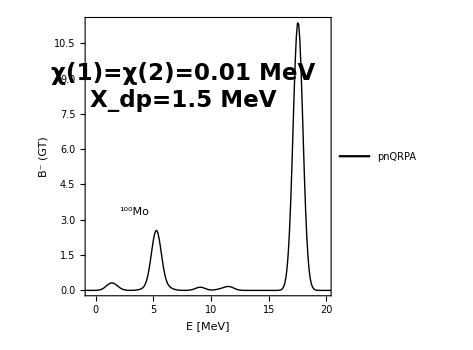

```mathematica
tableFig1=Table[{enBMMo[[i]],strBMMo[[i]]},{i,1,Length[strBMMo]}];
fig1=ListPlot[tableFig1,Joined->True,ImageSize->350,AspectRatio->1,Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],PlotStyle->{Thick,Black},PlotRange->{{-0.5,20},Full},FrameLabel->{"E [MeV]","B^- (GT)"},LabelStyle->{23,Bold,Black,FontFamily->"Times"},PlotLegends->Placed[{"pnQRPA"},{0.4,0.9}],Epilog->{Inset[Style["χ(1)=χ(2)=0.01 MeV",23,Bold,Black,FontFamily->"Times"],Scaled[{0.4,0.8}]],Inset[Style["X_dp=1.5 MeV",23,Bold,Black,FontFamily->"Times"],Scaled[{0.4,0.7}]],Inset[Framed[Style[Row[{Superscript["","100"],"Mo"}],23,Bold,Black,FontFamily->"Times"]],Scaled[{0.2,0.3}]]}];
Show[fig1]
Export["/Users/basavyr/Documents/Work/mathematica-useful-algorithms/Physics/Double-Beta-July-2022/pnQRPA_beta_transitions/exp_data_4/new_figs/fig1_set4.pdf",Show[fig1],ImageResolution->1200];
```

## Figure 2

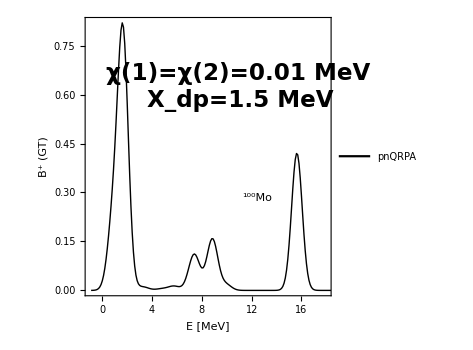

```mathematica
tableFig2=Table[{enBPMo[[i]],strBPMo[[i]]*1000},{i,1,Length[strBPMo]}];
fig2=ListPlot[tableFig2,Joined->True,ImageSize->350,AspectRatio->1,Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],PlotStyle->{Thick,Black},PlotRange->{{-1,18},Full},FrameLabel->{"E [MeV]","B^+ (GT)"},LabelStyle->{23,Bold,Black,FontFamily->"Times"},PlotLegends->Placed[{"pnQRPA"},{0.6,0.9}],Epilog->{Inset[Style["χ(1)=χ(2)=0.01 MeV",23,Bold,Black,FontFamily->"Times"],Scaled[{0.62,0.8}]],Inset[Style["X_dp=1.5 MeV",23,Bold,Black,FontFamily->"Times"],Scaled[{0.63,0.7}]],Inset[Framed[Style[Row[{Superscript["","100"],"Mo"}],23,Bold,Black,FontFamily->"Times"]],Scaled[{0.7,0.35}]]}];
Show[fig2]
Export["/Users/basavyr/Documents/Work/mathematica-useful-algorithms/Physics/Double-Beta-July-2022/pnQRPA_beta_transitions/exp_data_4/new_figs/fig2_set4.pdf",Show[fig2],ImageResolution->1200];
```

## Figure 3

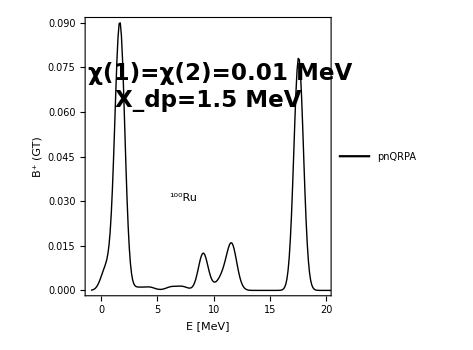

```mathematica
tableFig3=Table[{enBPRu[[i]],strBPRu[[i]]},{i,1,Length[strBPRu]}];
fig3=ListPlot[tableFig3,Joined->True,ImageSize->350,AspectRatio->1,Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],PlotStyle->{Thick,Black},PlotRange->{{-1,20},Full},FrameLabel->{"E [MeV]","B^+ (GT)"},LabelStyle->{23,Bold,Black,FontFamily->"Times"},PlotLegends->Placed[{"pnQRPA"},{0.5,0.9}],Epilog->{Inset[Style["χ(1)=χ(2)=0.01 MeV",23,Bold,Black,FontFamily->"Times"],Scaled[{0.55,0.8}]],Inset[Style["X_dp=1.5 MeV",23,Bold,Black,FontFamily->"Times"],Scaled[{0.5,0.7}]],Inset[Framed[Style[Row[{Superscript["","100"],"Ru"}],23,Bold,Black,FontFamily->"Times"]],Scaled[{0.4,0.35}]]}];
Show[fig3]
Export["/Users/basavyr/Documents/Work/mathematica-useful-algorithms/Physics/Double-Beta-July-2022/pnQRPA_beta_transitions/exp_data_4/new_figs/fig3_set4.pdf",Show[fig3],ImageResolution->1200];
```